```mathematica
SetDirectory @ NotebookDirectory[];
Import["QuEST.m"];
Install["quest_link_GPU"];
```

## Generating input states

```mathematica
ghzState[numQb_, {θ1_}] :=Join[
	{Subscript[Ry,0][π/2]},
	Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,numQb-2}],
	Table[Subscript[Rz, qb][θ1],{qb,0,numQb-1}]]
```

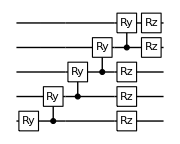

```mathematica
DrawCircuit @ ghzState[5, {0}]
```

```mathematica
squeezedState[numQb_, {θ1_,θ2_,θ3_}] := With[{
connec=Join[
Flatten[Table[{qb1,qb2},{qb1,0,numQb-2},{qb2,qb1+1,numQb-1}],1],Flatten[Table[{qb2,qb1},{qb1,0,numQb-2},{qb2,qb1+1,numQb-1}],1]]},
	Join[
		Table[Subscript[Ry, qb][π/2],{qb,0,numQb-1}],
		Table[Subscript[C, link⟦1⟧][Subscript[Rz, link⟦2⟧][θ1]],{link,connec}],
		Table[Subscript[Rx, qb][θ2],{qb,0,numQb-1}],
		Table[Subscript[Rz, qb][θ3],{qb,0,numQb-1}]]]
```

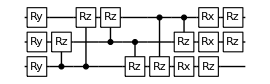

```mathematica
DrawCircuit @ squeezedState[3, {0,0,0}]
```

## Recomp input states

```mathematica
Subscript[pSwap, a_,b_] := Subscript[U, a,b][({{1, 0, 0, 0}, {0, 0, Exp[ⅈ #], 0}, {0, Exp[ⅈ #], 0, 0}, {0, 0, 0, 1}})]&

(* used for GHZ states *)
getRecompCircuit[n_] := Module[{gates},
gates = Flatten@ConstantArray[{Transpose @ Table[{Subscript[Rz, q],Subscript[Rx, q],Subscript[Ry, q],Subscript[Rz, q]},{q,0,n-1}], Table[Subscript[pSwap, q,Mod[q+1,n]], {q,0,n-1}]}, 2];
gates = Join[gates, Reverse[gates]];
AppendTo[gates, G];
MapThread[Compose, {gates, Table[Subscript[θ, t],{t,Length[gates]}]}]]
```

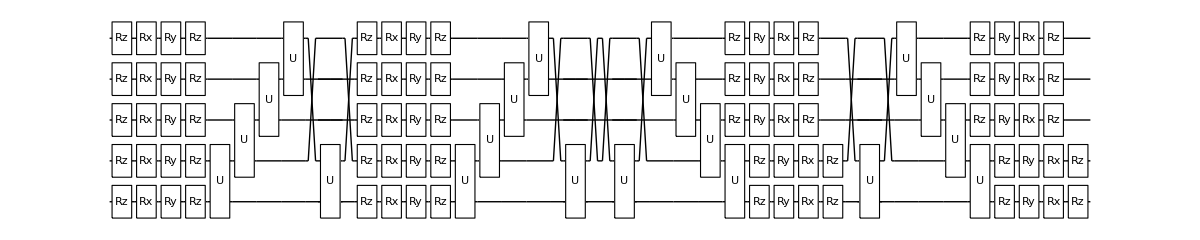

```mathematica
DrawCircuit[getRecompCircuit[5], 5]
```

```mathematica
(* used for squeezed-states *)
getRecompCircuit[n_] := Module[{gates},
gates = Flatten@ConstantArray[{Transpose @ Table[{Subscript[Rz, q],Subscript[Rx, q],Subscript[Ry, q],Subscript[Rz, q]},{q,0,n-1}], Table[Subscript[pSwap, q,Mod[q+1,n]], {q,0,n-1}]}, 2];
gates = Join[gates, Reverse[gates]];
AppendTo[gates, G];
MapThread[Compose, {gates, Table[Subscript[θ, t],{t,Length[gates]}]}]]
```

```mathematica
DrawCircuit[getRecompCircuit[5], 5]
```

-Graphics-

## Variational minimisation

```mathematica
calcEnergy[ψ_] :=
	1 - Abs[GetAmp[ψ, 0]]^2

calcEnergyGrad[ψ_, dψ_] :=
	Table[Re[CalcInnerProduct[ψ,dψdp] - Conjugate[GetAmp[ψ,0]] GetAmp[dψdp,0]],{dψdp, dψ}]
```

```mathematica
paramMapper = MapIndexed[Subscript[θ, #2⟦1⟧]->#1&];

sampleTimestep[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_] := (
	ApplyCircuit[bCirc /. paramMapper[θ + Δt Δθ], InitPureState[bψ, aψ]];
	calcEnergy[bψ] - prevE)

sampleTimesteps[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, {None,None,None}] :=
	Table[
		sampleTimestep[Δtchoice, θ, Δθ, prevE, aψ, bψ, bCirc],
		{Δtchoice, {Δt/2., Δt, 2.Δt}}];
	
sampleTimesteps[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, samples_List] :=
	If[
		samples⟦1⟧ === None,
		{sampleTimestep[Δt/2.,θ, Δθ, prevE, aψ, bψ, bCirc], samples⟦2⟧, samples⟦3⟧},
		{samples⟦1⟧, samples⟦2⟧, sampleTimestep[2.Δt, θ, Δθ, prevE, aψ, bψ, bCirc]}]

chooseTimestep[Δt_, θ_, Δθ_, prevE_, aψ_, bψ_, bCirc_, samples_:{None,None,None}] :=
	Module[{tA,tB,tC, tBest},
		{tA,tB,tC} = sampleTimesteps[Δt, θ, Δθ, prevE, aψ, bψ, bCirc, samples];
		tBest = Min[tA,tB,tC];
		Which[
			Abs[tBest] < 10^-8,
			Δt,
			tBest > 0,
			chooseTimestep[Δt/8., θ, Δθ, prevE, aψ, bψ, bCirc],
			tBest === tC,
			chooseTimestep[2.Δt, θ, Δθ, prevE, aψ, bψ, bCirc, {tB,tC,None}],
			tBest === tA,
			chooseTimestep[Δt/2., θ, Δθ, prevE, aψ, bψ, bCirc, {None,tA,tB}],
			tBest === tB,
			Δt]]
```

```mathematica
simImag[aψ_, bCirc_, bψ_, dψ_, initparams_, steps_, timestep_:Null] := Module[
	{params, matrA, vecC, energy, Δt, Δθ, energyLog={},paramLog={},ΔtLog={}},
		
		Δt = If[timestep === Null, 1, timestep];
		params = initparams;
		
		ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
		energy = calcEnergy[bψ];
		
		Do[
			CalcQuregDerivs[bCirc, aψ, params, dψ];
			matrA = Re @ CalcInnerProducts[dψ];

			ApplyCircuit[bCirc /. params, _fids_from_1[bψ, aψ]];
			vecC = - Re @ calcEnergyGrad[bψ, dψ];

			(* Δθ = LinearSolve[matrA, vecC]; *)
			Δθ = PseudoInverse[matrA] . vecC;
			Δt = If[
				timestep === Null,
				chooseTimestep[Δt, params⟦All,2⟧, Δθ, energy, aψ, bψ, bCirc],
				timestep];
			params = paramMapper[params⟦All,2⟧ + Δt Δθ];
		
			ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
			energy = calcEnergy[bψ];
			
			AppendTo[energyLog, energy];_fids_from_1
			AppendTo[paramLog, params⟦All,2⟧];
			AppendTo[ΔtLog, Δt];
		
			Null, steps];
			
		{energyLog, paramLog, ΔtLog}]
```

0.99756

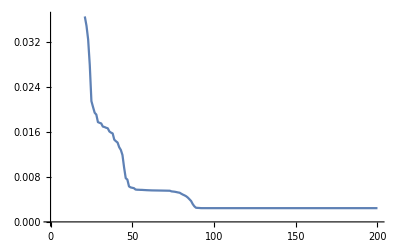

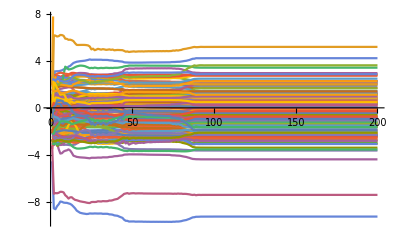

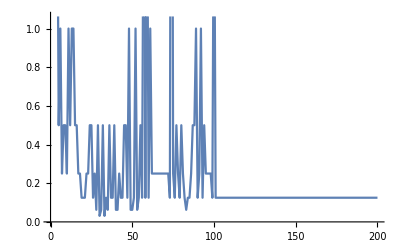

```mathematica
numQb = 6;
aCirc = squeezedState[numQb, RandomReal[{0,4π},3]];
bCirc = getRecompCircuit[numQb];
numParams = Length[bCirc]; (* bCirc⟦-1,1,2⟧ *)

{aψ, bψ} = CreateQuregs[numQb, 2];
dψ = CreateQuregs[numQb, numParams];

ApplyCircuit[aCirc, InitZeroState[aψ]];
initParams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}]; 
{energyLog, paramLog, ΔtLog} = simImag[aψ, bCirc, bψ, dψ, initParams, 200];
1 - calcEnergy[bψ]

ListLinePlot[
	energyLog
]
ListLinePlot[
	Transpose @ paramLog
]
ListLinePlot[
	ΔtLog 
]
```

```mathematica
DrawCircuit[aCirc, numQb]
DrawCircuit[bCirc, numQb]
```

DON' T DO MAX_ITERS: it' s a waste of time! 
Instead, detect convergence in the parameters and stop once converged (but ALSO set a max_iters just in case)

We can plot
- percentage converged to targetfid
- mean iterations to converge
- mean iterations to converge to targetfid

It first requires that we study param-convergence in a size-dependent way

STUDY OF CONVERGENCE:

```mathematica
simdata = <| "iterations"->500, "repeats"->5, "initNumQb"->3,"state"->"squeezed", "recompfids"->{}, "paramlogs"->{},"energylogs"->{}|>;

Do[
	DestroyAllQuregs[];
	bCirc = getRecompCircuit[numQb];
	numParams = Length[bCirc]; (*bCirc⟦-1,1,2⟧;*)
	{aψ, bψ} = CreateQuregs[numQb, 2];
	dψ = CreateQuregs[numQb, numParams];
	Echo[numQb, "numQb: "];

	{timing,data} = Timing @ Table[
		aCirc = squeezedState[numQb, RandomReal[{0,4π},3]];
		ApplyCircuit[aCirc, InitZeroState[aψ]];

		initParams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}]; 
		{energyLog, paramLog, ΔtLog} = simImag[aψ, bCirc, bψ, dψ, initParams, simdata["iterations"]];
		 {1 - calcEnergy[bψ], energyLog, paramLog},

		simdata["repeats"]
	];
        {fids,energyLogs,paramLogs} = Transpose[data];

	Echo[timing, "duration: "];
	AppendTo[simdata["recompfids"], fids];
	AppendTo[simdata["paramlogs"], paramLogs];
	AppendTo[simdata["energylogs"], energyLogs];

	Export["OLDNAMEWAS_convergencetest_squeezed_from_3.txt", simdata];

	Null,
	{numQb,simdata["initNumQb"],30}
]
```

numQb:  3

```mathematica
convergedata = Get["convergencetest_squeezed_from_3.txt"];
Keys @ convergedata
```

{iterations,repeats,initNumQb,state,recompfids,paramlogs,energylogs}

This seems to be an ok metric for convergence, i.e. it correlates well with plateaus in energy / fidelity, in their domains. On a [0,1] scale though, it appears very ‘late’.

```mathematica
getIterConverged[paramlog_] := With[{
	threshold=10^-4, 
	paramChangesEachIter= Transpose @ Abs[paramlog[[All,2;;]] - paramlog[[All,;;-2]]]},
	With[
	{pos=Position[paramChangesEachIter, _?(Max[#]<threshold&), 1]},
	If[Length[pos]==0, Length[paramChangesEachIter], pos[[1,1]]]
	]]
```

```mathematica
Manipulate[
		Column[ListLinePlot[
			1 - convergedata["energylogs"][[n,#]],
		GridLines->{
		{getIterConverged @ Transpose @ convergedata["paramlogs"][[n,#]]},{}}
		]& /@ Range[1,5]],
	{n,1,Length @ convergedata @ "energylogs", 1}
]
```

```mathematica
isConverged[prevparams_, params_] :=
	Max @ Abs[params⟦All,2⟧ - prevparams⟦All,2⟧] < 10^-4
```

```mathematica
simImagUntilConverged[aψ_, bCirc_, bψ_, dψ_, initparams_, maxsteps_, timestep_:Null] := Module[
	{params, prevparams, matrA, vecC, energy, Δt, Δθ, energyLog={},paramLog={},ΔtLog={}},
		
		Δt = If[timestep === Null, 1, timestep];
		params = initparams;
		prevparams = paramMapper[ConstantArray[0,Length[params]]]; (* starts > 10^-4 from params *)
		
		ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
		energy = calcEnergy[bψ];
		
		Do[
			CalcQuregDerivs[bCirc, aψ, params, dψ];
			matrA = Re @ CalcInnerProducts[dψ];

			ApplyCircuit[bCirc /. params, _fids_from_1[bψ, aψ]];
			vecC = - Re @ calcEnergyGrad[bψ, dψ];

			(* Δθ = LinearSolve[matrA, vecC]; *)
			Δθ = PseudoInverse[matrA] . vecC;
			Δt = If[
				timestep === Null,
				chooseTimestep[Δt, params⟦All,2⟧, Δθ, energy, aψ, bψ, bCirc],
				timestep];
			prevparams = params;
			params = paramMapper[params⟦All,2⟧ + Δt Δθ];
		
			ApplyCircuit[bCirc /. params, InitPureState[bψ, aψ]];
			energy = calcEnergy[bψ];
			
			AppendTo[energyLog, energy];
			AppendTo[paramLog, params⟦All,2⟧];
			AppendTo[ΔtLog, Δt];
			
			If[
				isConverged[prevparams,params],
				Break[]];
		
			Null, maxsteps];
			
		{energyLog, paramLog, ΔtLog}]
```

Simulating with full fidelity history, and convergence aborts

```mathematica
simdata = <|"maxiters"->500, "repeats"->20, "initNumQb"->3,"state"->"squeezed", "fidlogs"->{}, "paramlogs"->{}|>;

Do[
	DestroyAllQuregs[];
	bCirc = getRecompCircuit[numQb];
	numParams = Length[bCirc]; (*bCirc⟦-1,1,2⟧;*)
	{aψ, bψ} = CreateQuregs[numQb, 2];
	dψ = CreateQuregs[numQb, numParams];
	Echo[numQb, "numQb: "];

	{timing,data} = Timing @ Table[
		aCirc = squeezedState[numQb, RandomReal[{0,4π},3]];
		ApplyCircuit[aCirc, InitZeroState[aψ]];

		initparams = Table[Subscript[θ, t]->RandomReal@{-π,π}, {t,numParams}]; 
		{energyLog, paramLog, ΔtLog} = 
			simImagUntilConverged[aψ, bCirc, bψ, dψ, initparams, simdata["maxiters"]];
	     {Length[energyLog], energyLog, paramLog},

		simdata["repeats"]
	];
	{iters,energyLogs,paramLogs} = Transpose[data];

	Echo[timing, "duration: "];
	AppendTo[simdata["fidlogs"], 1-energyLogs];
	AppendTo[simdata["paramlogs"], paramLogs];

	Export["recomp_convergeabort_squeezed_from_3.txt", simdata];

	Null,
	{numQb,simdata["initNumQb"],30}
]
```

numQb:  3

duration:  122.456

numQb:  4

duration:  720.566

numQb:  5

duration:  6656.7

numQb:  6

duration:  5672.33

numQb:  7

duration:  5024.17

numQb:  8

duration:  3978.35

numQb:  9

duration:  7754.04

numQb:  10

duration:  7691.99

numQb:  11

duration:  7378.82

numQb:  12

duration:  10304.6

numQb:  13

duration:  12736.1

numQb:  14

duration:  12681.7

numQb:  15

duration:  16768.2

numQb:  16

duration:  18230.5

numQb:  17

duration:  18248.1

numQb:  18

duration:  14302.7

numQb:  19